# PHAS2443: Practical Mathematics II Exercises 3: Differential Equations

1. Write a generalised versions of the explicit Euler scheme, which will work for any function f(t,y) on the right-hand side of 
(dy(t))/dt= f(t,y)
(the function you write should take f as an argument), and use it to solve
(dy(t))/dt= t y(t)^2

with y(0)= - 1 over the range 0⩽t⩽10. Use timesteps of 1.0, 0.5 and 0.1, and plot your results for each case with the exact solution for comparison. This shows that the Euler method is capable of coping, in this case at least, with a nonlinear problem.

```mathematica
Clear[func, eScheme]

func[t_, y_] := t y^2

eScheme[f_, δt_, b_, tmax_]:= 
NestList[
{#[[1]] + δt, #[[2]] + δt f[#[[1]],#[[2]]]}&,
b,
Floor[tmax/δt]
]
```

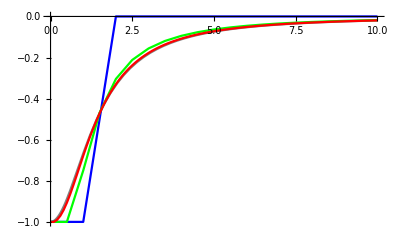

```mathematica
aSol = y[t] /. Flatten[DSolve[{y'[t] == t y[t]^2, y[0] == -1}, y[t], t]];

pAnalytic = Plot[aSol, {t, 0, 10}, PlotStyle-> RGBColor[0.5, 0.5, 0.5]];
p1 = ListPlot[eScheme[func, 1, {0, -1}, 10], PlotStyle-> Blue, Joined -> True];
p05 = ListPlot[eScheme[func, 0.5, {0, -1}, 10], PlotStyle-> Green, Joined -> True];
p01 = ListPlot[eScheme[func, 0.1, {0, -1}, 10], PlotStyle-> Red, Joined -> True];

Show[{pAnalytic, p1, p05, p01}]
```

2. Repeat question 1, for the same function and the same timesteps, for the Predictor-Corrector Euler method. This time, also plot for each time step the difference between the Euler solution and the exact solution, and between the Predictor-Corrector Euler method and the exact solution.

```mathematica
Clear[eCorrector]
eCorrector[f_, δt_, b_, tmax_] := 
NestList[
{
#[[1]] + δt,
#[[2]] + 
(δt / 2) (f[#[[1]], #[[2]]] + f[#[[1]] + δt, #[[2]] + δt f[#[[1]], #[[2]]]])} &,
b,
Floor[tmax/δt]
]
```

```mathematica
pAnalytic = Plot[aSol, {t, 0, 10}, PlotStyle-> RGBColor[0.5, 0.5, 0.5]];
pCorrected1 = ListPlot[eScheme[func, 1, {0, -1}, 10], PlotStyle-> Blue, Joined -> True];
pCorrected05 = ListPlot[eScheme[func, 0.5, {0, -1}, 10], PlotStyle-> Green, Joined -> True];
pCorrected01 = ListPlot[eScheme[func, 0.1, {0, -1}, 10], PlotStyle-> Red, Joined -> True];

Show[{pAnalytic, pCorrected1, pCorrected05, pCorrected01}]
```

-Graphics-

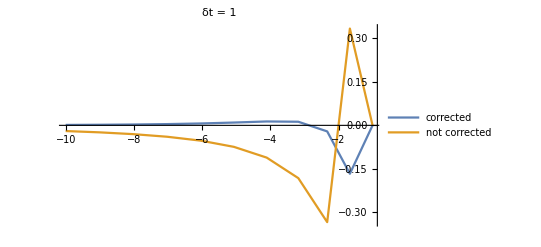

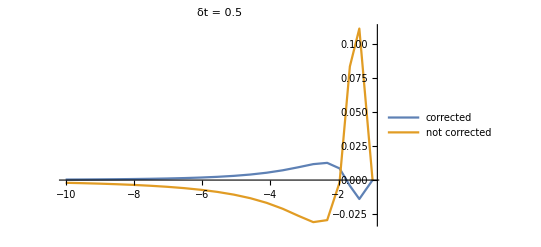

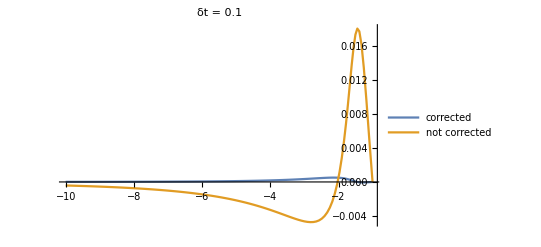

```mathematica
pDiff1 = ListPlot[
{Table[aSol, {t, 0, 10}] - eCorrector[func, 1, {0, -1}, 10],
Table[aSol, {t, 0,10}] -  eScheme[func, 1, {0, -1}, 10]},
 Joined -> True, PlotLegends -> {"corrected", "not corrected"}, PlotRange-> All, PlotLabel -> "δt = 1"]
pDiff05 = ListPlot[
{Table[aSol, {t, 0, 10, 0.5}] - eCorrector[func, 0.5, {0, -1}, 10],
Table[aSol, {t, 0,10, 0.5}] -  eScheme[func, 0.5, {0, -1}, 10]},
 Joined -> True, PlotLegends -> {"corrected", "not corrected"}, PlotRange-> All, PlotLabel -> "δt = 0.5"]
pDiff01 = ListPlot[
{Table[aSol, {t, 0, 10, 0.1}] - eCorrector[func, 0.1, {0, -1}, 10],
Table[aSol, {t, 0,10, 0.1}] -  eScheme[func, 0.1, {0, -1}, 10]},
 Joined -> True, PlotLegends -> {"corrected", "not corrected"}, PlotRange-> All, PlotLabel -> "δt = 0.1"]
```

3. Consider the system of stiff equations discussed in the lectures:
ⅆu/ⅆt= 998 u +1998 v
ⅆv/ⅆt= -999 u -1999 v
and set up a scheme to apply the Predictor-Corrector Euler algorithm to this system. Use this to solve the equations for boundary conditions u(0)=2 and v(0)= - 1, for 0 ⩽t ⩽1, using time steps of 0.1, 0.01 and 0.001.  What do you observe about the stability and the accuracy of this method compared with the forward Euler method?

A.H. Harker
Physics and Astronomy, UCL
September 2005, updated January 2009.